```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lorenzo/Phi4

```mathematica
m=1;
L=14;
ω[k_]:=Sqrt[m^2+k^2]
energy[klist_]:=Plus@@Map[ω,klist]
```

## g = 0.0001

```mathematica
(* Here I import the "discretized" wave function, after having appropriately "normalized" it
according to the occupation numbers and to the quantum numbers of the states *)
v =Import["data/wf3p_g=0.0001_L=14_E=20_nmax=3.csv","Data"];
data=ArrayReshape[v,{Length[v⟦1⟧]/3,3}];
data2=Select[data,(#⟦1⟧≥ 0)&];
```

```mathematica
(*Compare with the perturbative analytical wave function *)
f1[k1_,k2_,k3_]:=1/(m-(ω[k1]+ω[k2]+ω[k3]))1/Sqrt[ω[k1]ω[k2]ω[k3]m]
fit=Fit[data, pertWf[k1,k2,-k1-k2],{k1,k2}];
```

Experimental`NumericalFunction::dimsl: {k2} given in {k1,k2} should be a list of dimensions for a particular argument.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

```mathematica
Show[Plot3D[fit,{k1,-3,3},{k2,-3,3}],ListPointPlot3D[data,PlotStyle->PointSize[0.01]]]
```

-Graphics3D-

## g = 1, nmax=5

```mathematica
v =Import["data/wf3p_g=3_L=14_E=20_nmax=5.csv","Data"];
dataNmax5=ArrayReshape[v,{Length[v⟦1⟧]/3,3}];
data2=Select[dataNmax5,(#⟦1⟧≥ 0)&];
ListPointPlot3D[data2]
(* For nmax=5 there are additional features at k=0 *)
```

-Graphics3D-

## Ansatz

```mathematica
(* High-energy part of the wave function *)
Emax = 7;
wfh = Select[data,energy[#⟦1⟧,#⟦2⟧,-#⟦1⟧-#⟦2⟧]≥Emax&];
ListPointPlot3D[wfh,PlotRange-> All]
```

ListPointPlot3D::argx: ListPointPlot3D called with 0 arguments; 1 argument is expected.

ListPointPlot3D[{},PlotRange→All]

```mathematica
(* Ansatz for the tails *)
tailsNonSym={
1/energy[k1,k2,k3] 1/Sqrt[ω[k1]ω[k2]ω[k3]],
1/energy[k1,k2,k3]^2 1/Sqrt[ω[k1]ω[k2]ω[k3]]^2,
1/energy[k1,k2,k3]^3 1/Sqrt[ω[k1]ω[k2]ω[k3]]^3
(*,1/energy[k1,k2,k3] 1/Sqrt[ω[k1]ω[k2]ω[k3]]E^(-L^2 k1^2),
1/energy[k1,k2,k3] 1/Sqrt[ω[k1]ω[k2]ω[k3]]E^(-2L^2 k1^2)*)
};
(* Symmetrize w.r.t. momenta *)
symmetrize[expr_]:=Sum[expr/.{k1-> q⟦1⟧,k2-> q⟦2⟧,k3-> q⟦3⟧},{q,Permutations[{k1,k2,k3}]}]
tails=Map[symmetrize,tailsNonSym];
```

```mathematica
fit=Fit[wfh,tails/.{k3-> -k1-k2},{k1,k2}];
Show[
Plot3D[fit,{k1,-5,5},{k2,-5,5},PlotRange->{-0.003,0.}],
ListPointPlot3D[wfh]
]
```

ListPointPlot3D::argx: ListPointPlot3D called with 0 arguments; 1 argument is expected.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics3D-,ListPointPlot3D[{}]]

```mathematica
(* Plot the difference between fitted and numerical wave function *)
diff=Table[{x⟦1⟧,x⟦2⟧,x⟦3⟧-fit/.{k1-> x⟦1⟧,k2-> x⟦2⟧}},{x,wfh}];
ListPointPlot3D[diff]
```

ListPointPlot3D::argx: ListPointPlot3D called with 0 arguments; 1 argument is expected.

ListPointPlot3D[{}]

## k=0 behavior

```mathematica
datak0=Select[data,#⟦1⟧==0&&#⟦2⟧≥ 0&]⟦All,{2,3}⟧;
```

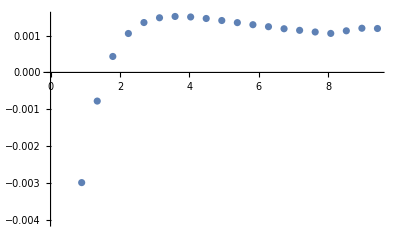

```mathematica
ListPlot[datak0]
```

```mathematica
datak0H=Select[datak0,#⟦1⟧≥ 4&];
fit=Fit[datak0H,1/x,x]
```

0.0075278384884782468/x

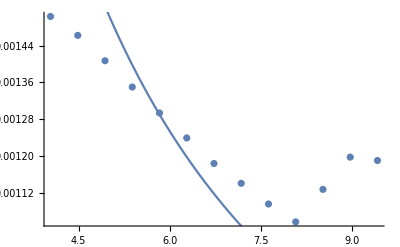

```mathematica
Show[ListPlot[datak0H],Plot[fit,{x,datak0H⟦1,1⟧,datak0H⟦-1,1⟧}]]
```

## g = 1, nmax=3

```mathematica
v =Import["data/wf3p_g=3_L=14_E=50_nmax=3.csv","Data"];
dataNmax3=ArrayReshape[v,{Length[v⟦1⟧]/3,3}];
data2=Select[data,(#⟦1⟧≥ 0)&];
ListPointPlot3D[data2]
(* We see that the function is smooth apart from the points k1=0, k2=0, k1+k2=0 *)
```

-Graphics3D-

```mathematica
x=dataNmax3⟦210,1⟧
```

-3.14159265358979312

```mathematica
dataNmax3d1=Select[dataNmax3,#⟦1⟧==x&];
dataNmax5d1=Select[dataNmax5,#⟦1⟧==x&];
```

```mathematica
max=Max[dataNmax5d1⟦All,2⟧]
```

9.42477796076937935

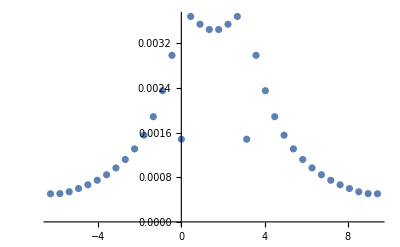

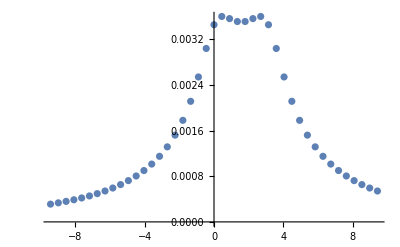

```mathematica
ListPlot[dataNmax5d1⟦All,{2,3}⟧,PlotRange-> All]
ListPlot[Select[dataNmax3d1⟦All,{2,3}⟧,Abs[#⟦1⟧]≤ max &],PlotRange-> All]
```

## Scratch

```mathematica
data=Table[{k1,k2,1/Sqrt[(ω[k1]*ω[k2]*ω[k1+k2])]1/(energy[{k1,k2,-k1-k2}])},{k1,-10,10,0.1},{k2,-10,10,0.1}]
```

{{{-10.,-10.,0.000554167},{-10.,-9.9,0.000561113},{-10.,-9.8,0.000568196},{-10.,-9.7,0.000575418},{-10.,-9.6,0.000582784},{-10.,-9.5,0.000590298},190,{-10.,9.6,0.00470843},{-10.,9.7,0.00474265},{-10.,9.8,0.00475719},{-10.,9.9,0.00474889},{-10.,10.,0.00471587}},200}
 |  |  |  |

```mathematica
ListPointPlot3D[data]
```

-Graphics3D-

```mathematica
ListPointPlot3D[1/Sqrt[(ω[k1]*ω[k2]*ω[k1+k2])]1/(energy[{k1,k2,-k1-k2}]),{k1,-10,10},{k2,-10,10}]
```

ListPointPlot3D::nonopt: Options expected (instead of {k2,-10,10}) beyond position 1 in ListPointPlot3D[1/(√(√(1+k1^2) √(1+k2^2) √(1+Plus[«2»]^2)) (√(1+k1^2)+√(1+Plus[«2»]^2)+√(1+k2^2))),{k1,-10,10},{k2,-10,10}]. An option must be a rule or a list of rules.

ListPointPlot3D[1/(√(√(1+k1^2) √(1+k2^2) √(1+(k1+k2)^2)) (√(1+k1^2)+√(1+(-k1-k2)^2)+√(1+k2^2))),{k1,-10,10},{k2,-10,10}]

```mathematica
ϵ=0;
f[k_?NumericQ]:=NIntegrate[1/(ω[q1]ω[q2]) 1/(energy[{q1,q2,k}]-ϵ)/.{q2-> k-q1},{q1,-Infinity,Infinity}]
```

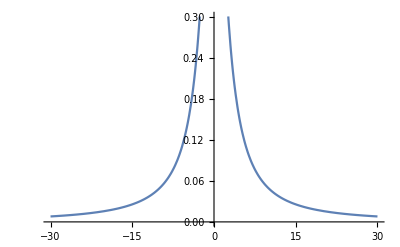

```mathematica
Plot[f[k],{k,-30,30}]
```

```mathematica
f1[k1_,k2_,k3_]:=1/(ω[k1]+ω[k2]+ω[k3])1/Sqrt[ω[k1]ω[k2]ω[k3]]
f2[k1_?NumericQ,k2_?NumericQ,k3_?NumericQ]:=f2 [k1,k2,k3]=f1[k1,k2,k3]*(f[k1]+f[k2]+f[k3])
```

```mathematica
Emax=20;
wfh = Select[data2,energy[{#⟦1⟧,#⟦2⟧,-#⟦1⟧-#⟦2⟧}]≥Emax&];
Max[Abs[wfh⟦All,3⟧]]
```

0.000639948604613302233

```mathematica
ListPointPlot3D[wfh]
```

-Graphics3D-

```mathematica
fit=Fit[wfh,{f1[k1,k2,-k1-k2],f2[k1,k2,-k1-k2]},{k1,k2}]
```

0.178162/(√(√(1+k1^2) √(1+(-k1-k2)^2) √(1+k2^2)) (√(1+k1^2)+√(1+(-k1-k2)^2)+√(1+k2^2)))-(0.0554768 (NIntegrate[1/((ω[q1] ω[q2]) (energy[{q1,q2,k1}]-ϵ))/.{q2→k1-q1},{q1,-∞,∞}]+NIntegrate[1/((ω[q1] ω[q2]) (energy[{q1,q2,-k1-k2}]-ϵ))/.{q2→(-k1-k2)-q1},{q1,-∞,∞}]+NIntegrate[1/((ω[q1] ω[q2]) (energy[{q1,q2,k2}]-ϵ))/.{q2→k2-q1},{q1,-∞,∞}]))/(√(√(1+k1^2) √(1+(-k1-k2)^2) √(1+k2^2)) (√(1+k1^2)+√(1+(-k1-k2)^2)+√(1+k2^2)))

```mathematica
diff=Table[{e⟦1⟧,e⟦2⟧,(fit/.{k1-> e⟦1⟧,k2-> e⟦2⟧})-e⟦3⟧},{e,wfh}];
```

```mathematica
ListPointPlot3D[diff,PlotRange->All]
```

-Graphics3D-